#### INSTRUCTIONS: Run common_funs.nb, ES_FindSymGroups.nb, chooseTmat.nb, then this notebook

#### Choose Tmat and display some output

```mathematica
Tmat=TmatBrownNew;
```

```mathematica
Tmat=TmatIgel;
```

```mathematica
Tmat=TmatMar17;
```

```mathematica
Tmat==Transpose[Tmat]
MatrixNote[Tmat]
PrintVoigt[Tmat]
```

## The superlattice

```mathematica
WantDetails="WantDetails";
```

#### Do not change these. (But you might want to change ListΣ below.)

```mathematica
ListSigmaAll={TRIV,MONO,ORTH,TET,CUBE,ISO,XISO,TRIG};
```

```mathematica
ListSigmaXISO={TRIV,MONO,ORTH,TET,XISO,ISO};
```

#### Closest Tmat for each Sigma symmetry class (Pathway 2) This is not needed if it has already been done in BC_CumulativeBeta.nb

```mathematica
OutputFor[Tmat,#]&/@ListSigmaAll;
```

#### Be sure the Nodes all have decimal points. No integers. That is, 4., not 4, and 2., not 2

```mathematica
ww=1;ww=1.2;
Clear[SigmaOfPt];
SigmaOfPt[{x_,y_}]:="";
Node[ISO]  :={0.,5-.5};    SigmaOfPt[Node[ISO]]  ="ISO";
Node[XISO]:={-1ww,4.};   SigmaOfPt[Node[XISO]]="XISO";
Node[TRIG]:={-1ww,2.5};SigmaOfPt[Node[TRIG]]="TRIG";
Node[CUBE]:={   1ww,4.};  SigmaOfPt[Node[CUBE]]="CUBE";
Node[TET]  :={  1ww,3.};   SigmaOfPt[Node[TET]]  ="TET";
Node[ORTH]:={  1ww,2.};   SigmaOfPt[Node[ORTH]]="ORTH";
Node[MONO]:={0.,1+.5};  SigmaOfPt[Node[MONO]]="MONO";
Node[TRIV]:={0.,0+.5};  SigmaOfPt[Node[TRIV]]="TRIV";
dummy;
```

```mathematica
LatticeBlank:={Arrowheads[.0008],Thickness[.0015],Dashing[{.013,.013}],
{Arrow[{Node[TRIV],Node[MONO]},.25]},  (* from TRIV to MONO *)
{Arrow[{Node[MONO],Node[ORTH]},.25]},  (* from MONO to ORTH *)
{Arrow[{Node[ORTH],Node[TET]},.2]},   (* from ORTH *)
{Arrow[{Node[TET],Node[CUBE]},.2]},   (* from TET to CUBE *)
{Arrow[{Node[TRIG],Node[XISO]},.2]},   (* from TRIG to XISO *)
{Arrow[{Node[TET],Node[XISO]},.3]},   (* from TET to XISO *)
{Arrow[{Node[TRIG],Node[CUBE]},.3]},   (* from TRIG to CUBE *)
{Arrow[{Node[MONO],Node[TRIG]},.3]},   (* from MONO to TRIG *)
{Arrow[{Node[CUBE],Node[ISO]},.25]},   (* from CUBE to ISO *)
{Arrow[{Node[XISO],Node[ISO]},.25]}  (* from XISO to ISO *)
};
```

## Here is where the 8 balls from BC_CumulativeBeta.nb could enter.

#### Pathway 2: nodes of lattice are closest Sigma to Tmat (TRIV)

```mathematica
SmatOfPt[Node[TRIV]]=Tmat;
SmatOfPt[Node[MONO]]=Closest[Tmat,MONO];
SmatOfPt[Node[ORTH]]=Closest[Tmat,ORTH];
SmatOfPt[Node[TET]]  =Closest[Tmat,TET];
SmatOfPt[Node[XISO]]=Closest[Tmat,XISO];
SmatOfPt[Node[ISO]]  =Closest[Tmat,ISO];
SmatOfPt[Node[TRIG]]=Closest[Tmat,TRIG];SmatOfPt[Node[CUBE]]=Closest[Tmat,CUBE];
```

#### Pathway 3: path through lattice is specified, then each node is the closest Tmat to the previous node

```mathematica
Clear[ClosestToPrevious];
ClosestToPrevious[0,Tmat_]:=Tmat;
ClosestToPrevious[i_,Tmat_]:=ClosestToPrevious[i,Tmat]=Closest[ClosestToPrevious[i-1,Tmat],ListSigmaXISO[[i+1]]];
```

#### This block will engage Pathway 3

```mathematica
(* OutputFor[ClosestToPrevious[0,Tmat],MONO]
OutputFor[ClosestToPrevious[1,Tmat],ORTH]
OutputFor[ClosestToPrevious[2,Tmat],TET]
OutputFor[ClosestToPrevious[3,Tmat],XISO]
OutputFor[ClosestToPrevious[4,Tmat],ISO]
SmatOfPt[Node[TRIV]]=Tmat;
SmatOfPt[Node[MONO]]=ClosestToPrevious[1,Tmat];
SmatOfPt[Node[ORTH]]=ClosestToPrevious[2,Tmat];
SmatOfPt[Node[TET]]  =ClosestToPrevious[3,Tmat];
SmatOfPt[Node[XISO]]=ClosestToPrevious[4,Tmat];
SmatOfPt[Node[ISO]]  =ClosestToPrevious[5,Tmat];
SmatOfPt[Node[TRIG]]=Closest[Tmat,TRIG];SmatOfPt[Node[CUBE]]=Closest[Tmat,CUBE]; *)
```

## Densify the number of maps on a chosen path

#### Specify the discretization increment between symmetry classes (TRIV to ISO) The path indices will depend on dt and can be found from the lattice diagram below.

```mathematica
dt=0.5;
PathXISO={6,7,8,12,14,15,16,10,3,5,11}; 
PathCUBE={6,7,8,12,14,15,16,17,18,13,11}; 
PathTRIG={6,7,8,4,1,9,18,13,11};
```

```mathematica
dt=0.2;
PathTRIG={19,20,21,22,23,24,16,13,9,7,1,10,17,29,33,48,37,34,30,26,25}; 
PathCUBE={19,20,21,22,23,24,27,31,35,36,38,39,40,41,42,43,44,45,46,47,48,37,34,30,26,25}; 
PathXISO={19,20,21,22,23,24,27,31,35,36,38,39,40,41,42,43,32,28,15,11,6,8,12,14,18,25};
```

#### Choose one:

```mathematica
PathX=PathXISO;
```

#### Defining the points in the lattice and the elastic map at each point. t = 0 represents the lower-symmetry end of the segment (TRIV) t = 1 represents the higher-symmetry end of the segment (ISO)

```mathematica
PointsAndSmat:=Union[ Flatten[Table[{
{(1-t)Node[TRIV]+t Node[MONO],(1-t)SmatOfPt[Node[TRIV]]+t SmatOfPt[Node[MONO]]},
{(1-t)Node[MONO]+t Node[ORTH],(1-t)SmatOfPt[Node[MONO]]+t SmatOfPt[Node[ORTH]]},
{(1-t)Node[ORTH]+t Node[TET],  (1-t)SmatOfPt[Node[ORTH]]+t SmatOfPt[Node[TET]]},
{(1-t)Node[TET]  +t Node[XISO],(1-t)SmatOfPt[Node[TET]]  +t SmatOfPt[Node[XISO]]},
{(1-t)Node[TET]  +t Node[CUBE],(1-t)SmatOfPt[Node[TET]]  +t SmatOfPt[Node[CUBE]]},
{(1-t)Node[XISO]+t Node[ISO],  (1-t)SmatOfPt[Node[XISO]]+t SmatOfPt[Node[ISO]]},
{(1-t)Node[MONO]+t Node[TRIG],(1-t)SmatOfPt[Node[MONO]]+t SmatOfPt[Node[TRIG]]},
{(1-t)Node[TRIG]+t Node[XISO],(1-t)SmatOfPt[Node[TRIG]]+t SmatOfPt[Node[XISO]]},
{(1-t)Node[TRIG]+t Node[CUBE],(1-t)SmatOfPt[Node[TRIG]]+t SmatOfPt[Node[CUBE]]},
{(1-t)Node[CUBE]+t Node[ISO],  (1-t)SmatOfPt[Node[CUBE]]+t SmatOfPt[Node[ISO]]}},{t,0,1,dt}],1]];
```

```mathematica
points=#[[1]]&/@PointsAndSmat;
Length[points]
```

#### Here are the points and their positions in the list. (If the crossing points are superimposed, you can perturb SigmaOfPt above.)

```mathematica
points
Graphics[{LatticeBlank,PointSize[.03],
Point/@points,
Text[Style[Position[points,#],12],#+{.3,0}]&/@points},ImageSize->200]
```

#### Save. This next line finishes the definition of SmatOfPt

```mathematica
(SmatOfPt[#[[1]]]=#[[2]])&/@PointsAndSmat;  (* SAVE *)
```

#### Example: Point 3 in the lattice (closest XISO for dt = 0.5)

```mathematica
points[[3]]
MatrixForm[SmatOfPt[points[[3]]]]
```

#### Example: the initial Tmat

```mathematica
MatrixForm[Tmat]
MatrixForm[SmatOfPt[points[[6]]]]
```

#### Example: point 8 (closest MONO for dt = 0.5)

```mathematica
MatrixForm[Closest[Tmat,MONO]]
MatrixForm[SmatOfPt[points[[8]]]]
```

#### Example: all matrices in a path

#### One Tmat on the XISO path

```mathematica
MatrixForm[SmatOfPt[points[[PathX[[5]]]]]]
```

#### Display the set of Tmats as BB and as Voigt (for a chosen path)

```mathematica
(
Print["point ",#," (", Length[PathX]," total)"];
PrintVoigt[SmatOfPt[points[[#]]]];Print["betaTRIV = ",Round[MakeReal[AngleMatrix[SmatOfPt[Node[TRIV]],SmatOfPt[points[[#]]]]/Degree],0.01]];
Print["betaMONO = ",Round[MakeReal[AngleMatrix[SmatOfPt[Node[MONO]],SmatOfPt[points[[#]]]]/Degree],0.01]];
Print["betaISO = ",Round[MakeReal[AngleMatrix[SmatOfPt[Node[ISO]],SmatOfPt[points[[#]]]]/Degree],0.01]];
Print["------------------------------------------------------------"];
)&/@PathX
```

## Beta and lattice preliminaries. Beta curves

#### Any 999s in the Beta8tuple/Degree mean you have not run the needed OutputFor. Path points are any of the chosen points, not just the nodes.

```mathematica
βT[Tmat_,Σ_]:=999Degree;   (* This should have been entered in FindSymGroupsForPublic *)
βofPathPt[{x_,y_},Σ_]:=βT[SmatOfPt[{x,y}],Σ];  (* Measures how far the elastic map at (x,y) is from having symmetry Σ *)
Beta8tuple[pt_]:=βofPathPt[pt,#]&/@ListSigmaAll;
```

```mathematica
NodeList=Node/@ListSigmaAll;
xyIsNode[{x_,y_}]:=MemberQ[NodeList,{x,y}];   (* A statement, either true or false *)
```

#### As functions of integer n. The integer n will give the point (n, 0) on the horizontal axis in the diagrams. It runs over 1, 2, 3, ..., Length[path].

```mathematica
PathPtOfN[n_,path_]:=points[[path[[n]]]];   
βofN[n_,path_,Σ_]:=βofPathPt[PathPtOfN[n,path],Σ];   (* Measures how far the elastic map at n is from having symmetry Σ *)
PtOnβcurve[n_,path_,Σ_]:={n,βofN[n,path,Σ]/Degree};   (* vertical coordinate is in degrees *)
BetaCurve[Σ_,path_]:={Point/@Table[PtOnβcurve[n,path,Σ],{n,1,Length[path]}],
                                                       Line[Table[PtOnβcurve[n,path,Σ],{n,1,Length[path]}]]}(* vertical coordinate is in degrees *);
(* βatLastPtOnCurve[path_,Σ_]:=βofN[Length[path],path,Σ]/Degree  (* in degrees *) *)
βatFirstPtOnCurve[path_,Σ_]:=βofN[1,path,Σ]/Degree  (* in degrees *)
nIsNode[n_,path_]:=xyIsNode[PathPtOfN[n,path]];  (* A statement, either true or false *)
NlistForNodes[path_]:=Select[Range[Length[path]],nIsNode[#,path]&];
SigmaOfN[n_,path_]:=SigmaOfPt[PathPtOfN[n,path]](* The symmetry class Σ for the elastic map at n *)
```

```mathematica
VerticalLineAtN[n_,path_,Σ_]:=Line[{{n,0},PtOnβcurve[n,path,Σ]}];   (* vertical coordinate is in degrees *)VerticalLinesForΣ[path_,Σ_]:=VerticalLineAtN[#,path,Σ]&/@Select[Range[1,Length[path]],xyIsNode[points[[path[[#]]]]]&];
```

#### Examples :

```mathematica
PathX
PathX[[4]]
PathPtOfN[4,PathX]
Beta8tuple[PathPtOfN[4,PathX]]
```

```mathematica
Length[PathX]
Range[Length[PathX]]
PathPtOfN[#,PathX]&/@Range[Length[PathX]] 
Select[%,xyIsNode]
nIsNode[#,PathX]&/@Range[Length[PathX]]
```

```mathematica
βatFirstPtOnCurve[PathX,ISO]
βatFirstPtOnCurve[PathX,XISO]
βatFirstPtOnCurve[PathX,MONO]
```

#### check: closest-MONO point should have betaMONO = 0

```mathematica
βofN[8,PathX,MONO]
```

#### Again, any 999s in the 8-tuples/Degree mean you have not run all OutputFor. When you run the lattice for the first time you will see lots of 999s.

```mathematica
pickpoint=12;
MatrixNote[Tmat]
ListSigmaAll
Graphics[{LatticeBlank,PointSize[.015],
Point/@points,
{Red,
Arrow[{points[[pickpoint]],Node[#]},.1]&/@ListSigmaAll},
If[True,Text[Style[Round[Beta8tuple[#]/Degree,.01],13],#,{-1.15,0}]&/@points]},ImageSize->900]
Graphics[{LatticeBlank,PointSize[.03],
Point/@points,
Text[Style[Position[points,#],12],#+{.3,0}]&/@points},ImageSize->200]
```

#### KEY COMMAND: Specify the beta curves to be plotted.

```mathematica
ListΣ={ORTH,ISO};
```

```mathematica
ListΣ={ISO,MONO};
```

```mathematica
ListΣ={MONO,ORTH,TET,TRIG,XISO,CUBE,ISO};
```

#### Optional: Determine the scale for the y-value of the custom tick labels on the x-axis

```mathematica
yText[PathX_,RangeΣ_]:=Max[βofPathPt[points[[PathX[[1]]]],#]&/@RangeΣ]/Degree;
yran=yText[PathX,ListΣ]
```

#### MAIN DIAGRAM The last text command places a label like β_XISO^ (15.98) on the y-axis hues are set in chooseTmat.nb

```mathematica
ptsz=0.013;
ytick1=-0.07 yran;
ytick2=2 ytick1;
BetaCurvesDiagram[path_,ListΣ_]:=Graphics[{PointSize[ptsz],
{hue[#],BetaCurve[#,path]}&/@ListΣ, (* colored segmented beta curves *)
{Dashing[{.01,.02}],VerticalLinesForΣ[path,#]&/@ListΣ}, (* vertical lines *)
Text[Style[path[[#]],10],{#,ytick1}]&/@Range[Length[path]], (* integer tick label (e.g., 8) *) 
Text[Style[SigmaOfN[#,path],11],{#,ytick2}]&/@NlistForNodes[path], (* tick label as path entry (e.g., TET) *)
Text[Style[SequenceForm[BetaText[#]," (",Round[βatFirstPtOnCurve[path,#],0.01],")"],{hue[#],15}], (* the text *)
                                                           {1-0.05Length[path],βatFirstPtOnCurve[path,#]},{1,0}]&/@ListΣ, (* the location of the text *)
Text[Style["β_Σ, degrees",22],{1-0.35Length[path],.5yText[path,ListΣ]},{0,0},{0,1}]  (* y-axis label *)
},  
Axes->True,Ticks->{None,Automatic},AxesOrigin->{1,0},TicksStyle->12,AspectRatio->1,ImageSize->500]
```

#### OutputAllPts[Sigma] will give the beta values for the specified Sigma and for all the points.

```mathematica
OutputAllPts[Σ_]:=OutputFor[SmatOfPt[#],Σ]&/@points;
```

#### KEY COMMAND : this will execute OutputAllPts for all specified Sigmas Progress can be tracked by checking which Sigma the calculation is on (see order in ListΣ)

```mathematica
WantDetails="NoWantDetails";
```

```mathematica
(* OutputAllPts/@{ORTH} *)
```

```mathematica
(* OutputAllPts/@{XISO} *)
```

```mathematica
OutputAllPts/@ListΣ
```

### Show one path for a single symmetry class You can always add the lattice to the right, as shown here. If you want node indices on the x-axis, uncomment the relevant line in BetaCurvesDiagram above.

```mathematica
MatrixNote[Tmat]
GraphicsRow[{
BetaCurvesDiagram[PathX,{XISO}],
Graphics[{LatticeBlank,PointSize[.03],
Point/@points,
{PointSize[.01],Point/@{{0,-.3},{0,5.5}}},
Text[Style[Position[points,#],12],#+{.3,0}]&/@points}]},ImageSize->800,Spacings->0]
```

### Show one path for a single symmetry class

```mathematica
BetaCurvesDiagram[PathX,{XISO}]
```

### The betaMONO curves tends to reveal the most problematic maps

```mathematica
BetaCurvesDiagram[PathX,{MONO}]
```

### Just to be ornery: pick an oddball path that doesn’t make much sense

```mathematica
(* path={8,12,14,16,10,2,1}; BetaCurvesDiagram[path,{XISO}] *)
```

### Show two paths for a single symmetry class

```mathematica
Show[{
BetaCurvesDiagram[PathXISO,{XISO}],
BetaCurvesDiagram[PathCUBE,{XISO}]}]
```

### Display all chosen Sigma curves for the path through XISO

```mathematica
BetaCurvesDiagram[PathXISO,ListΣ]
```

### Display all chosen Sigma curves for the path through CUBE

```mathematica
BetaCurvesDiagram[PathCUBE,ListΣ]
```

### Display all chosen Sigma curves for the paths through CUBE and XISO

```mathematica
Show[{
BetaCurvesDiagram[PathXISO,ListΣ],
BetaCurvesDiagram[PathCUBE,ListΣ]}]
```

### Display all chosen Sigma curves for the path through TRIG

```mathematica
BetaCurvesDiagram[PathTRIG,ListΣ]
```

## For reference: Igel

### Pathway 2 through XISO (Igel)

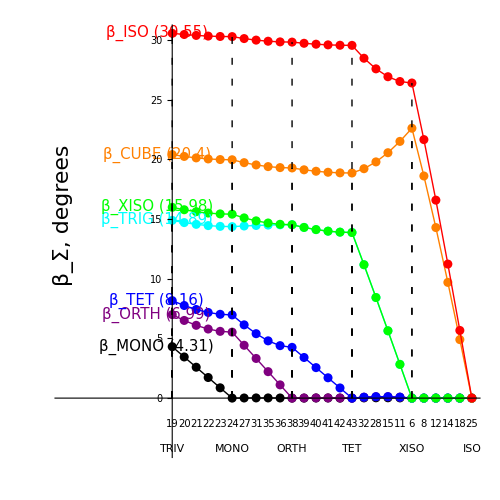

### Pathway 2 through CUBE (Igel)

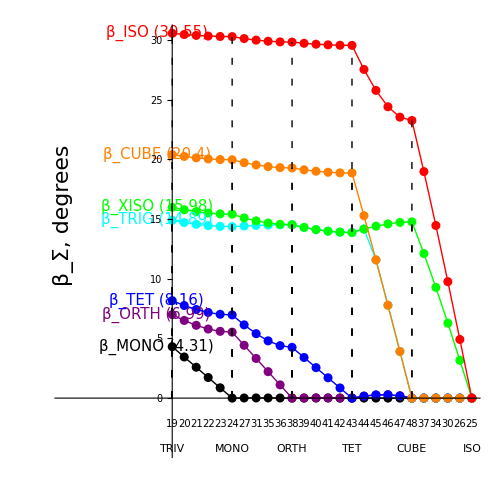

### Pathway 2 through TRIG (Igel)

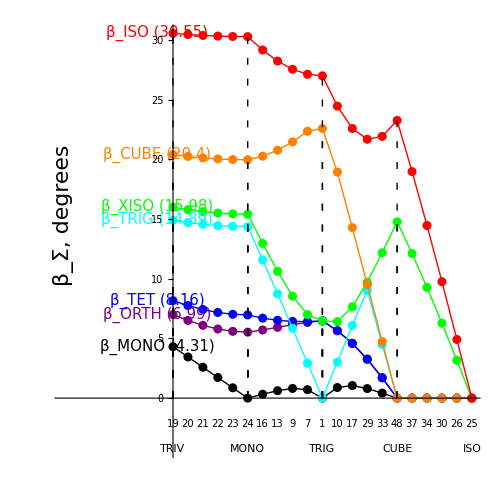

### Pathway 3 through XISO (Igel)

### Pathway 3 through CUBE (Igel)

### Pathway 3 through TRIG (Igel)

## For reference: Brown

### Pathway 2 through XISO (Brown)

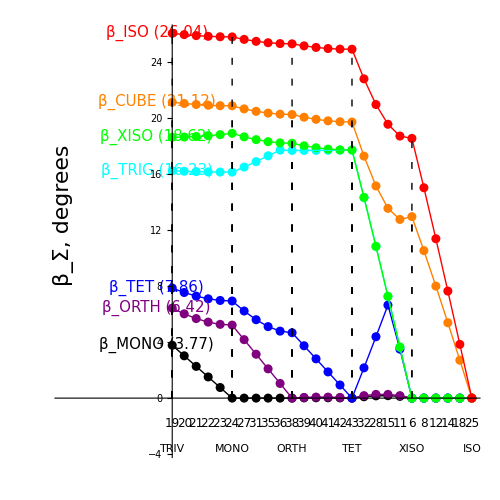

### Pathway 2 through CUBE (Brown)

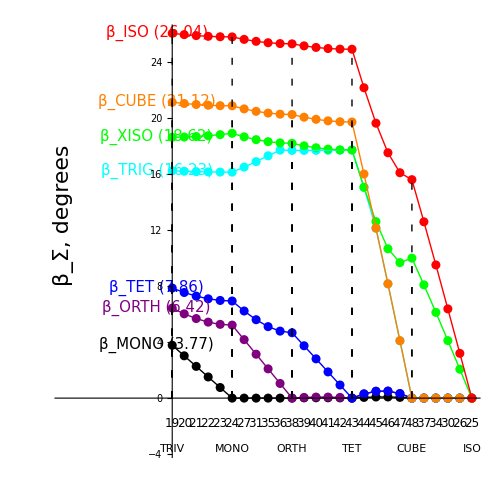

### Pathway 2 through TRIG (Brown)

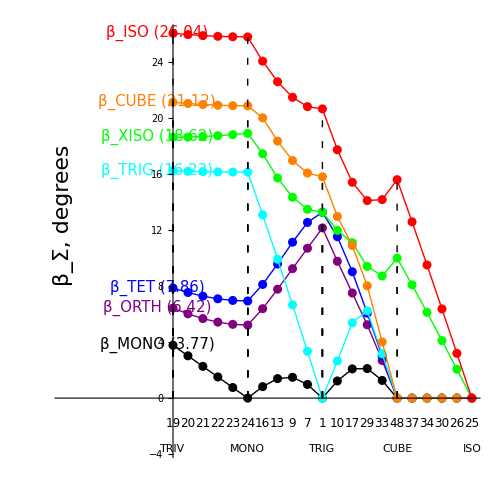

### Pathway 3 through XISO (Brown)

### Pathway 3 through CUBE (Brown)

### Pathway 3 through TRIG (Brown)

## For reference: TmatMar17

### Pathway 2 through XISO (TmatMar17)

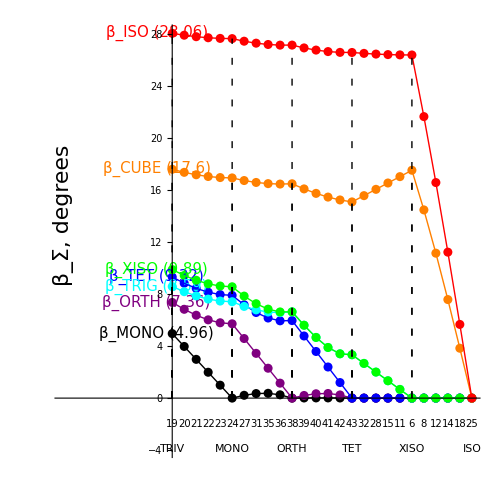

### Pathway 2 through CUBE (TmatMar17)

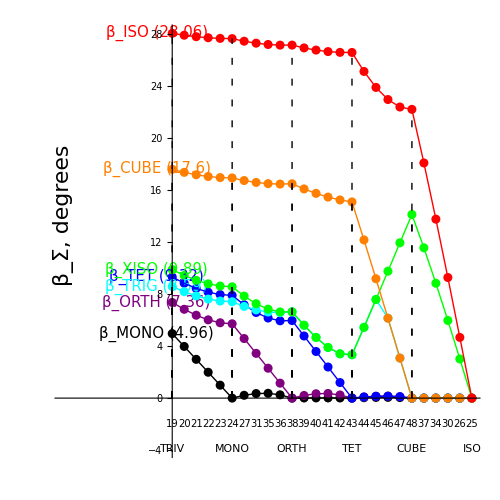

### Pathway 2 through TRIG (TmatMar17)

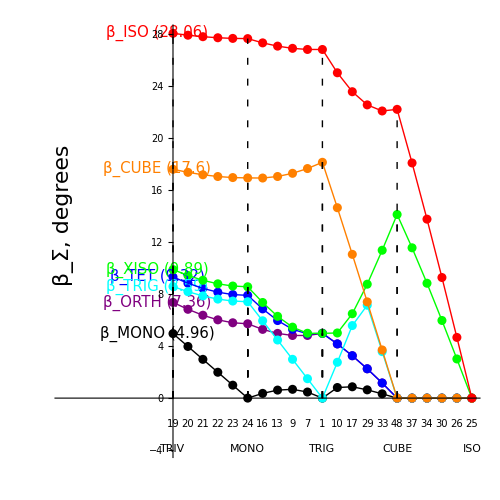

### Pathway 3 through XISO (Mar17)

### Pathway 3 through CUBE (Mar17)

### Pathway 3 through TRIG (Mar17)

## Super lattice for Igel

### Beta angles for Igel Pathway 2 (target point is 12, halfway between MONO and ORTH for dt = 0.5)

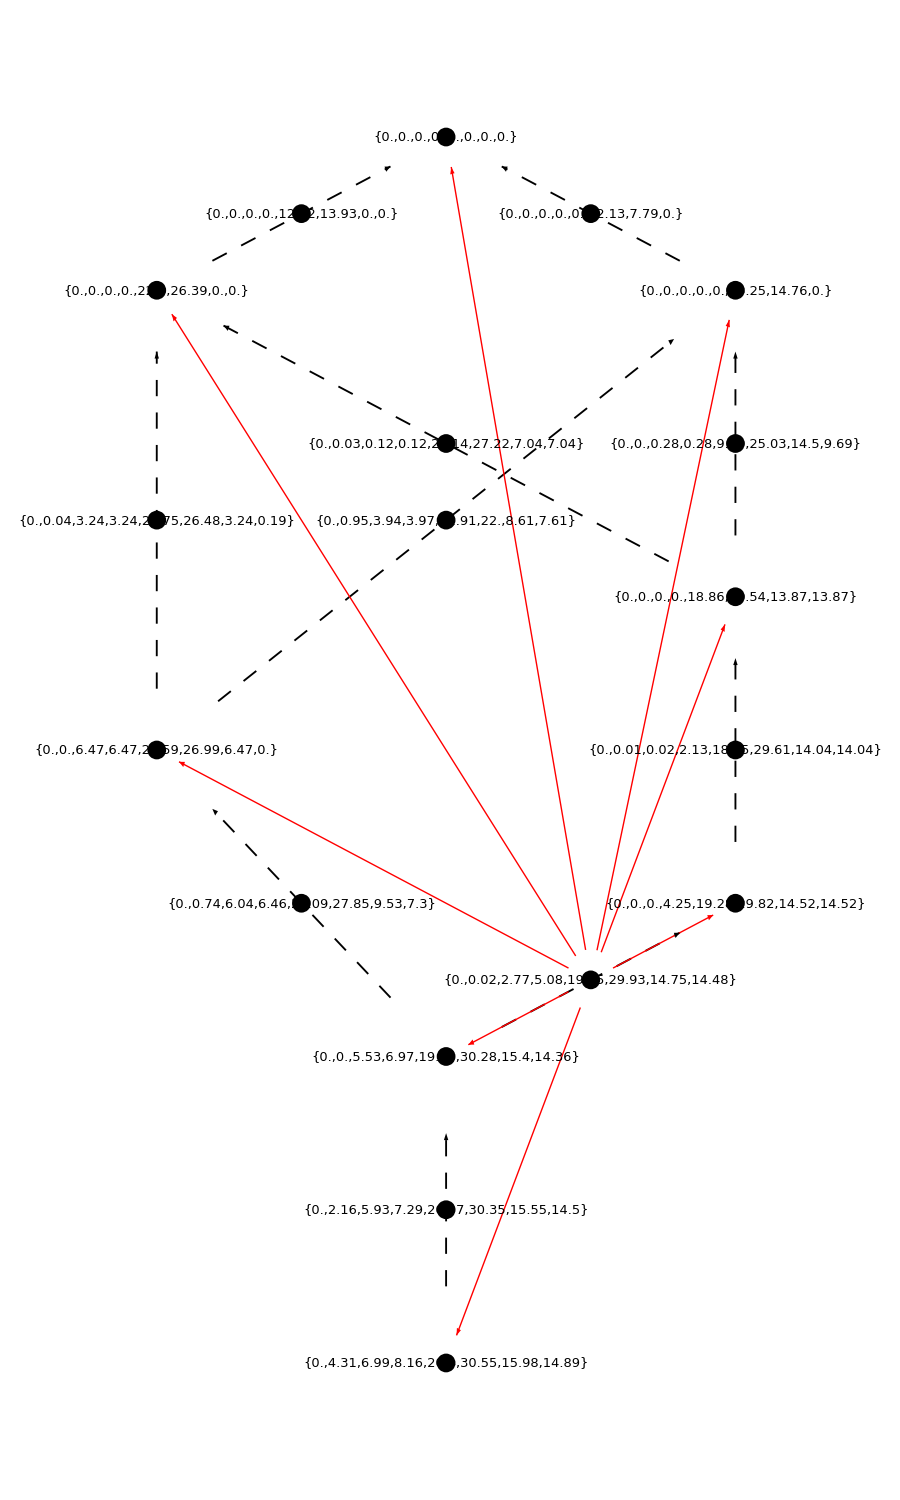

## Super lattice for Brown

### Beta angles for Brown Pathway 2 (target point is 12, halfway between MONO and ORTH for dt = 0.5)

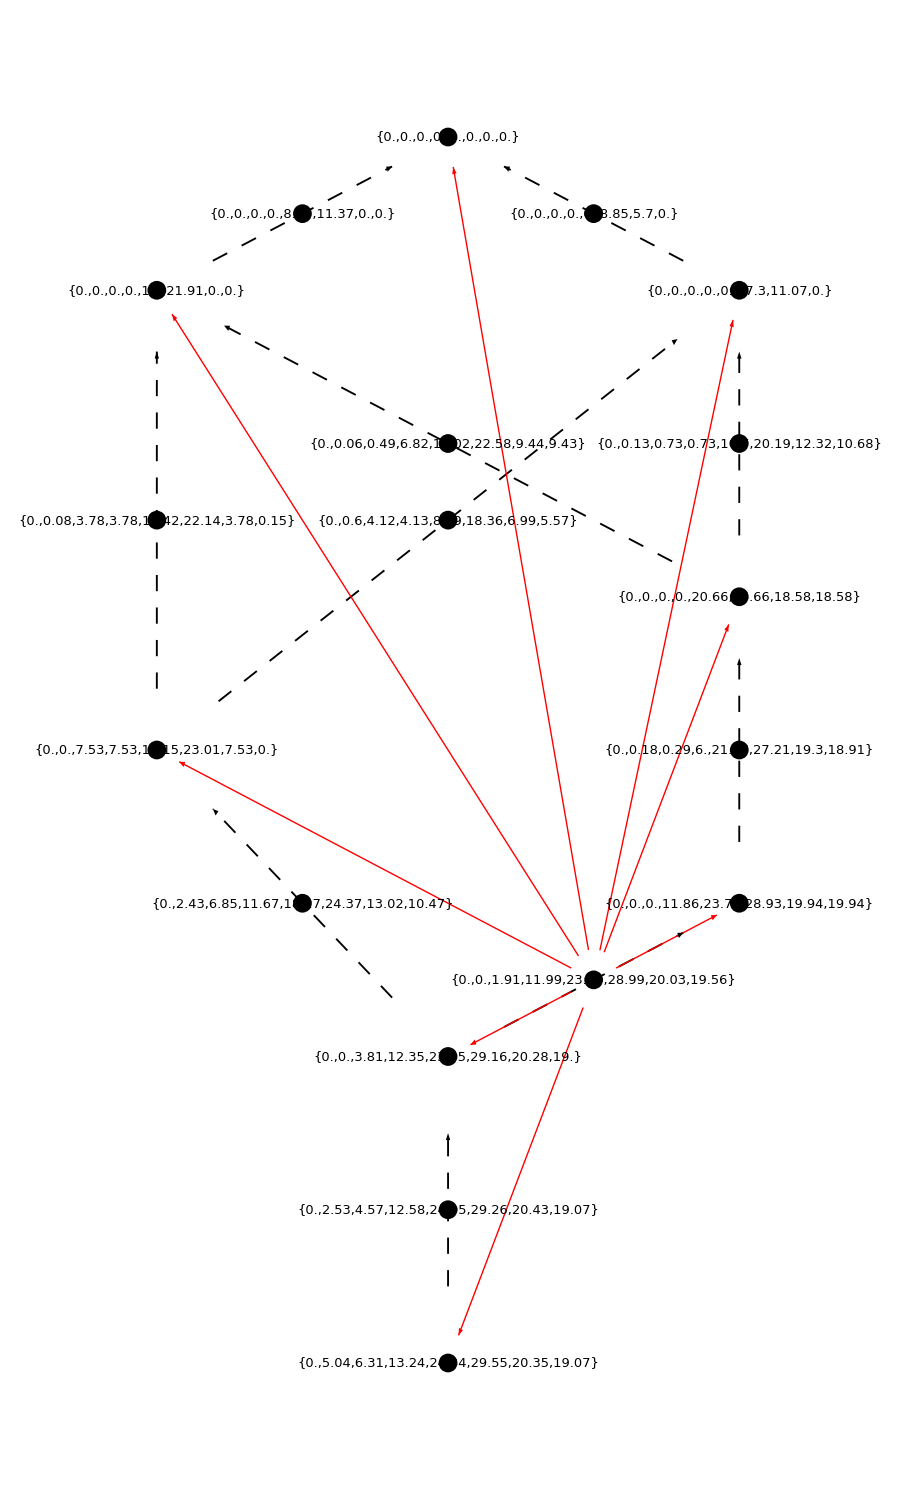

## Super lattice for TmatMar17

### Beta angles for TmatMar17 Pathway 2 (target point is 12, halfway between MONO and ORTH for dt = 0.5)